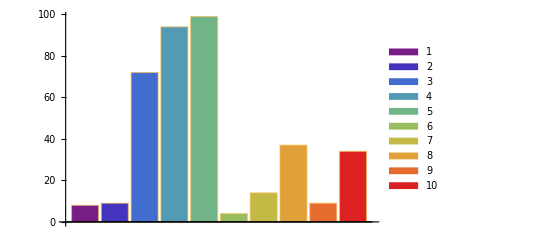

-Graphics-

-Graphics-

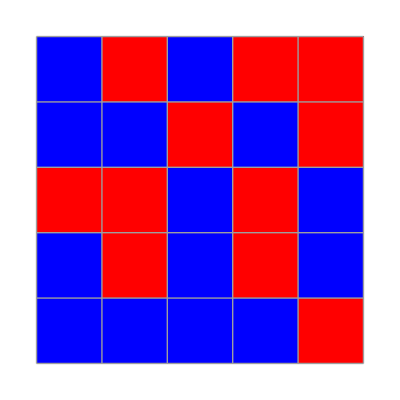

-Graphics-

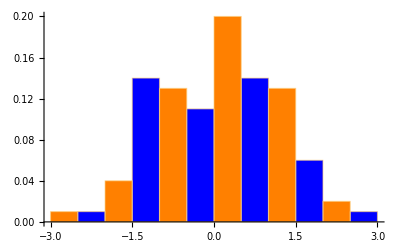

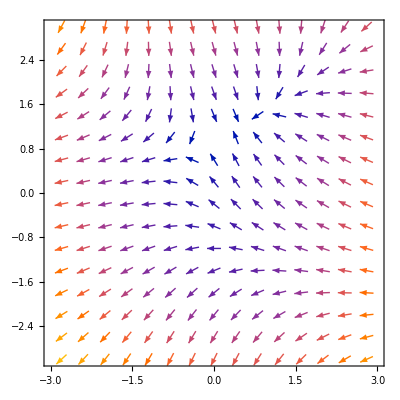

```mathematica
data=RandomInteger[{1,100},10];
BarChart[data,ChartStyle->"Rainbow",ChartLegends->Automatic]

data=RandomInteger[{2,3},5];
PieChart[data,ChartStyle->"Pastel",ChartLegends->Automatic]

data=Table[{RandomReal[{1,3}],RandomReal[{1,3}],RandomReal[{1,3}]},{30}];
BubbleChart[data,ChartStyle->"DarkRainbow",BubbleSizes->{0.1,0.2}]

matrix=RandomInteger[{1,2},{5,5}];
ArrayPlot[matrix,ColorRules->{1->Blue,2->Red},Mesh->True]

data=Table[{RandomInteger[{1,3}],RandomInteger[{2,4}]},{5}];
SectorChart[data,ChartStyle->"NeonColors",ChartBaseStyle->EdgeForm[Thick]]

data=RandomVariate[NormalDistribution[],100];
Histogram[data,10,"Probability",ChartStyle->{Orange,Blue}]

vectorField={-1-x^2+y,1+x-y^2};
VectorPlot[vectorField,{x,-3,3},{y,-3,3},ColorFunction->Automatic,VectorScale->{0.03,0.9,None}]
```

```mathematica
Manipulate[
RiemannSum=Sum[Sin[(i-1) Pi/n] (Pi/n),{i,1,n}];
Plot[{Sin[x],
Sin[Ceiling[x n/Pi-1/2] Pi/n]*UnitStep[Sin[x]]
},
{x,0,Pi},
Filling->{2->Axis},
PlotRange->{{0,Pi},{0,1}},
PlotLegends->{"sin(x)","Riemann Sum"},
PlotLabel->Row[{
"Riemann sum for n = ",n," is ",N[RiemannSum],
", Error = ",N[Integrate[Sin[x],{x,0,Pi}]-RiemannSum]
}],
AxesLabel->{"x","y"}
],
{{n,5,"Number of Rectangles"},1,50,1,Appearance->"Labeled"}
]
```

```mathematica
Manipulate[
Module[
{f,a,x1,x2,secantLine,tangentLine},
f[x_]:=x^2;
a=1;
x1=a;
x2=a+h;
secantLine[x_]:=(f[x2]-f[x1])/(x2-x1) (x-x1)+f[x1];
tangentLine[x_]:=2 a (x-a)+f[a];
Plot[
{f[x],secantLine[x],tangentLine[x]},
{x,0,2},
PlotRange->{{0,2},{0,4}},
Epilog->{Red,PointSize[Large],Point[{x1,f[x1]}],Point[{x2,f[x2]}]},
PlotLegends->{"f(x) = x^2","Secant Line","Tangent Line"},
AxesLabel->{"x","y"},
PlotLabel->Style[Row[{"h = ",h}],14],
PlotStyle->{Automatic,Blue,Green}]
],
{{h,0.1,"Distance (h)"},0.01,1,0.01}
]
```